```mathematica
Needs["Constants`"]
Needs["Capture`"]
Needs["Utilities`"]
Needs["EnergyLoss`"]
Needs["Dielectrics`"]
```

## Δr

#### Read EL dicts

Nuclear

```mathematica
FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];
```

Electronic

```mathematica
(*FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIwiderm"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIwiderm"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIwiderm"];*)
FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];
```

#### Interpolation test

```mathematica
SiO2eELDict[["f"]]=TestInterpolation[SiO2eELDict]
MgOeELDict[["f"]]=TestInterpolation[MgOeELDict]
```

Set::noval: Symbol SiO2eELDict in part assignment does not have an immediate value.

TestInterpolation[SiO2eELDict]

Set::noval: Symbol MgOeELDict in part assignment does not have an immediate value.

TestInterpolation[MgOeELDict]

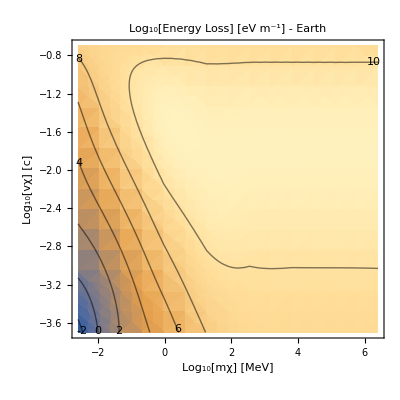

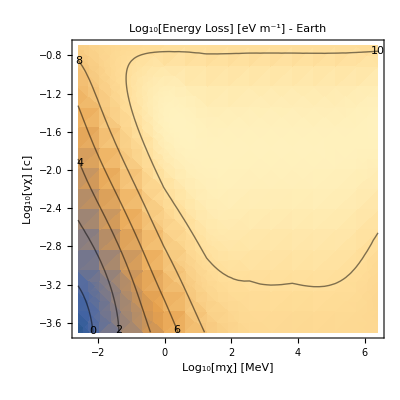

```mathematica
PlotEL[SiO2eELDict]
PlotEL[MgOeELDict]
```

#### EL functions

Organize into an EL function

Mantle

```mathematica
fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)
```

Core

```mathematica
fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]
feELCore[mχ_,vχ_]:=FeeELDict[["f"]][mχ,vχ]
```

```mathematica
FeeELDict[["f"]]
```

InterpolatingFunction[…]

```mathematica
FeNuc0ELDict[["f"]][-32.3,4.8]
FeNuc0ELDict[["f"]][-32.3,4.8]
```

-3.42349

```mathematica
10^-32("c")^2/("JpereV")/.SIConstRepl
10^-23("c")^2/("JpereV")/.SIConstRepl
```

5617.98

5.61798×10^12

### Test initialization functions

#### Propagating to the Earth

```mathematica
EK∞[mχ_,v∞_]:= 1/2 mχ (v∞)^2
```

```mathematica
E∞[mχ_,v∞_,r∞_,V_]:=EK∞[mχ,v∞]+V[r∞]
```

```mathematica
E∞[mχ,v∞,r∞,V[x,y,#]&]
```

EK∞[mχ,v∞]+V[x,y,r∞]

```mathematica
Vtest[r_]:=Gα/r
E∞[mχ,v∞,r∞,Vtest]
```

Gα/(r∞)+(mχ (v∞)^2)/2

```mathematica
vperp[v∞_,b∞_,r_]:=(b∞ v∞)/r
```

```mathematica
vr[mχ_,v∞_,b∞_,r∞_,V_,r_]:=√(2/mχ(E∞[mχ,v∞,r∞,V]-V[r])-vperp[v∞,b∞,r]^2)
```

```mathematica
vr[mχ,v∞,b∞,r∞,V,r]
```

√(-((b∞)^2 (v∞)^2)/r^2+(2 ((mχ (v∞)^2)/2-V[r]+V[r∞]))/mχ)

```mathematica
br[mχ_,v∞_,b∞_,r∞_,V_,r_]:=(b∞)/(√(1+(V[r∞]-V[r])/(EK∞[mχ,v∞])))
```

```mathematica
br[mχ,v∞,b∞,r∞,V,r]
```

(b∞)/(√(1+(2 (-V[r]+V[r∞]))/(mχ (v∞)^2)))

```mathematica
"G"/.SIConstRepl
```

6.67×10^-11

```mathematica
Vgrav[r_,mχ_] :=- (mχ("G"/.SIConstRepl)("ME"/.EarthRepl))/r
```

```mathematica
Vgrav[#,mχ]&
%[r]
```

Vgrav[#1,mχ]&

-(3.98199×10^14 mχ)/r

#### Example of Initial conditions

```mathematica
1/("rE"/.EarthRepl)br["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

0.499653

so barely changed, electrons are fast, but did decrease (which is the right direction)

```mathematica
vr["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

260048.

```mathematica
vperp["c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,"rE"/.EarthRepl]
```

150000.

#### Δr

```mathematica
Clear[Δrtest]
Δrtest[mχ_,vχ_,κ_,y_,consts_] :=(y 1/2 mχ vχ^2)/(κ^2 "JpereV"10^fELMantle[Log10[mχ], Log10[vχ]]) /.consts
```

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-9,10^-2,SIConstRepl]
%/("rE"/.EarthRepl)
```

1734.54

0.000272255

```mathematica
dE[rE_,bE_]:=2 √(rE^2-bE^2)
```

```mathematica
dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

1.10349×10^7

```mathematica
N[1/500]
```

0.002

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-10,10^-2,SIConstRepl]/dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

0.0157187

So at 10^-10mixing at electron mass and halo speeds, with b∞ = 1/2 rE, we are in intermediate scattering regime

#### Δr generalised (e only)

```mathematica
dc[bE_] := 2 √(rcore^2-bE^2)
dE[bE_] := 2 √(REarth^2-bE^2)
dM[bE_]:= If[rcore^2>bE^2,dE[bE] - dc[bE],Re[dE[bE]]]
```

```mathematica
dM[0]+dc[0]
REarth 2
```

1.2742×10^7

1.2742×10^7

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
ΔrAveraged[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
fΔrAveraged[mχ_,vχ_]:=Log10[ΔrAveraged[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

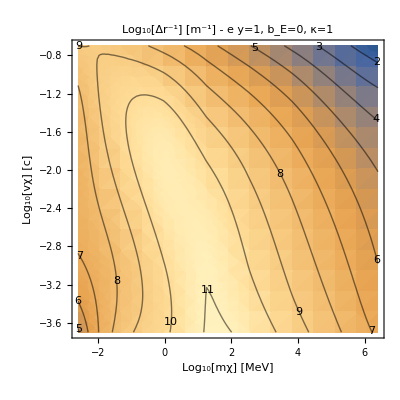

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveraged;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - e y=1, b_E=0, κ=1"]
]
```

#### Δr total

```mathematica
ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
(*fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]*)
fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

```mathematica
FeeELDict[["kinlist"]][["mχ"]]("c")^2/("JpereV")/.SIConstRepl
```

{2500.,48267.4,931898.,1.79921×10^7,3.47374×10^8,6.70674×10^9,1.29487×10^11,2.5×10^12}

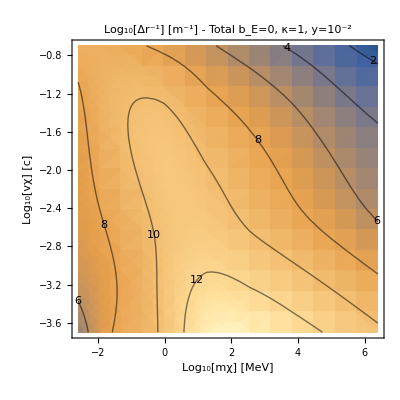

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveragedTot0;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - Total b_E=0, κ=1, y=10^-2"]
]
```

4.81365+6.04929×10^-19 ⅈ

-3.69897

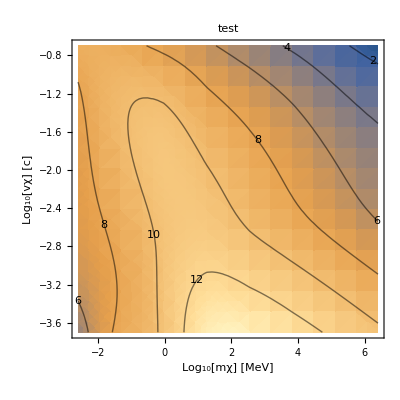

```mathematica
Block[{ELdict},
ELdict=FeeELDict;
ELdict[["f"]]=fΔrAveragedTot0;
(*PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - Total b_E=0, κ=1, y=10^-2"]*)
Print[ELdict[["f"]][Log[10,First[ELdict[["kinlist"]][["mχ"]]]],Log[10,First[ELdict[["kinlist"]][["vχ"]]]]]];
Print[N[Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]]];
Print[Show[{DensityPlot[Re[ELdict[["f"]][m+6 - Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v +Log10["c"/.Constants`SIConstRepl]]],
  		{m,Log[10,First[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl]},
  		{v,Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},
  		FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[mχ] [MeV]","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[vχ] [c]"},PlotLabel->"test"],
  ContourPlot[Re[ELdict[["f"]][m+6- Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]]],
  		{m,Log[10,First[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl]},
  		{v,Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},
  		ContourLabels->True,ContourShading->False]}]]
]
```

#### Explain boundary and peak (lowest kinetic energy above the fermi energy)

```mathematica
("EF")/("JpereV") /.FeeELDict[["fitparams"]]
("EF")/("JpereV") /.SiO2eELDict[["fitparams"]]
("EF")/("JpereV") /.MgOeELDict[["fitparams"]]
```

{8.0607,12.1265,20.9318,78.9,2030.5,42688.4}

{20.0443,58.1666}

{10.3207,18.4045,21.0279,50.3071}

```mathematica
((10^-2.5 "c")^2"m")/("JpereV") /.FeeELDict[["fitparams"]]
((10^-1.5 "c")^2 10^-2"m")/("JpereV") /.FeeELDict[["fitparams"]]
```

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

#### Interaction Length

```mathematica
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,
vχtemp,FeeELDict[["fitparams"]],βcore]& [1/2]];
(*NIntegrate[dσdEReNum[ω,mχtemp,vχtemp,FeTotalparams,βcore],{ω,0,ωmaxtemp}]*)
]
```

0.0262616

tesing cell input

```mathematica
σFe = 1.085089955014962*^13
```

1.08509×10^13

```mathematica
σtemp = 0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,vχtemp,FeTotalparams,βcore]& []];
(*σtemp = NIntegrate[dPdωeNum[ω,mχtemp,vχtemp,SiO2Totalparams],{ω,0,ωmaxtemp}]*)
]
```

0

```mathematica
lFe = κ^2("nI"/.SIcoreparams)σFe /.κ->10^-10(*approx, should really do density of each shell*)
```

1.52116×10^22

1.51848×10^15

0.

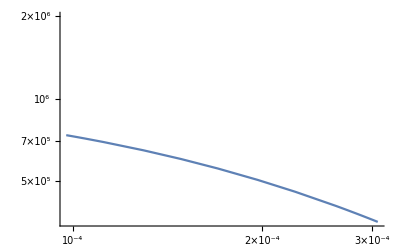

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
```

```mathematica
nIFromDensity[3580, "mN" /. SiNucCoeffs]
```

7.70224×10^28

```mathematica
1/(2 "ℏ")(2.5 10^7 ("JpereV")/("c")^2) (2.5 10^-5 "c")^2/.SIConstRepl
```

1.18632×10^13

```mathematica
SIcoreparams
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.1215×10^30,qF→3.2142×10^10,vF→3.72227×10^6,μ→6.31108×10^-18,ωp→5.97822×10^16,α→1/137,χ→0.432735,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→83.5454,nI→1.40188×10^29,Z→8,M→9.27329×10^-26,EF→6.31108×10^-18}

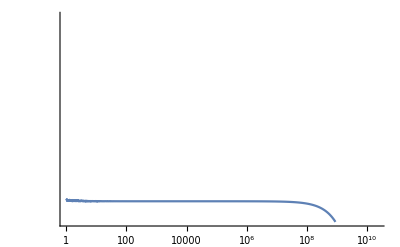

```mathematica
LogLogPlot[dPdωNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcoreparams)|>],{ω,10^0,10^15},PlotRange->{0,2.5 10^8}]
```

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
(*Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];*)
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
σtemp = 0;
Clear[SiNuc0σ]
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
```

1.51848×10^15

0.

2.90748×10^10

3.15401×10^16

```mathematica
((κ^2/.κ->10^-10)SiNuc0PTot)/((nIFromDensity[3580,"mN"/.SiNucCoeffs])("ℏ"/.SIConstRepl)(10^-3 "c"/.SIConstRepl))
```

0.000129382

9.5117×10^8

```mathematica
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
SiNuc0Pλ=(((κ^2/.κ->10^-10)SiNuc0PTot)/(10^-3 "c"/.SIConstRepl))^-1
```

2.90748×10^10

3.15401×10^16

9.5117×10^8

So from Nuclear Si at 0 temperature, the scattering length is large compared to the Earth

```mathematica
dPdωNuc0Num[# ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]& [1/2]
```

```mathematica
SiNucCoeffs
```

<|a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171×10^-15,mN→4.648×10^-26|>

```mathematica
FrontEndTokenExecute@"Save"
```

### Unit testing for MC capture code

Psuedo code

We need to store the following to describe the state of the particle

globally we need 
(r,v_r,v_(⊥1),v_(⊥1)) with b the impact parameter and r the radial position in the earth

at each time step we need
l interaction length
i_int which process to interact with (electrical or nuclear)
velocity of target
	speed of target (sampled from distribution function)
	point on sphere - for velocity of target
E_R recoil energy 
	q momentum transfer
	scattering angle of DM particle
New velocity
	azimuthal angle 
	polar calculated from scattering angle

#### Update v

```mathematica
vr[r_,E_,V_,m_,vp_]:=√(Simplify[2/m E]-2/m V[r]-vp)
V[r_]:=-("α")/r
```

```mathematica
(*Clear[modv,Δt,vr]*)
Block[{m,r,v={vr,vp1,vp2},l,speed,Δt,Δr,L,vp,E},
speed = √(v.v);
Δt = l/speed;
Δr = Δt v[[1]];

E=m/2 speed^2;
vp = v.DiagonalMatrix[{0,1,1}].v;
(*L = m r vp;*)
v[[1]]=vr[r+Δr,E,V,m,vp];
v

]
```

{√(vr^2+(2 α)/(m (r+(l vr)/(√(vp1^2+vp2^2+vr^2))))),vp1,vp2}

```mathematica
√(-vp1^2-vp2^2+(2 (1/2 m (vp1^2+vp2^2+vr^2)-("α")/(r+(l vr)/(√(vp1^2+vp2^2+vr^2)))))/m)
```

#### compute l - interaction length

#### σ

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
dσdERNuc0[]
```

```mathematica
?dσdERNuc0
```

## new

#### Load parameters

```mathematica
Clear[FeTotalparams,SiO2Totalparams,MgOTotalparams]
```

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

#### Load Interaction Length

```mathematica
Clear[FeλeDictSI,SiO2λeDictSI,MgOλeDictSI]
```

```mathematica
(*FeλeDictSI = ReadIt[NotebookDirectory[]<>"FeλeDictSI"];
SiO2λeDictSI = ReadIt[NotebookDirectory[]<>"SiO2λeDictSI"];
MgOλeDictSI = ReadIt[NotebookDirectory[]<>"MgOλeDictSI"];*)
FeλeDictSI = ReadIt[NotebookDirectory[]<>"FeλeDictSI_total"];
SiO2λeDictSI = ReadIt[NotebookDirectory[]<>"SiO2λeDictSI_total"];
MgOλeDictSI = ReadIt[NotebookDirectory[]<>"MgOλeDictSI_total"];
```

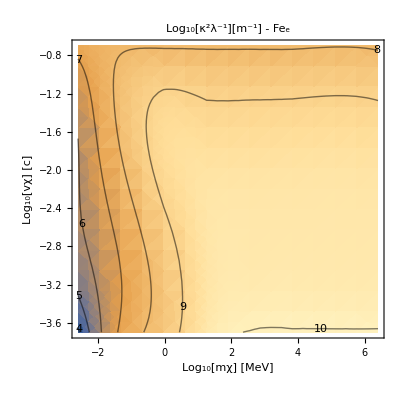

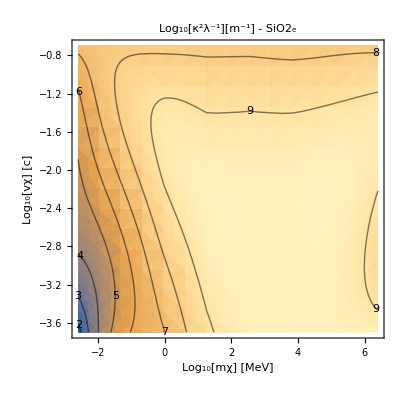

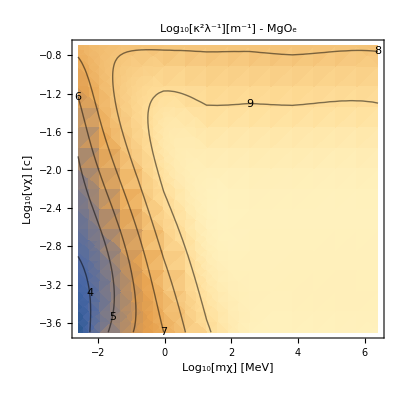

```mathematica
EnergyLoss`PlotEL[FeλeDictSI,"Fe_e",True,"Log_10[κ^2λ^-1][m^-1] - Fe_e"]
EnergyLoss`PlotEL[SiO2λeDictSI,"SiO2_e",True,"Log_10[κ^2λ^-1][m^-1] - SiO2_e"]
EnergyLoss`PlotEL[MgOλeDictSI,"MgO_e",True,"Log_10[κ^2λ^-1][m^-1] - MgO_e"]
```

### Unit Test

#### Interaction length

```mathematica
FeλeDictSI[["f"]]
FeλeDictSI[["f"]][-25,6]
```

InterpolatingFunction[…]

9.69693

```mathematica
(*testl[mχ_,vχ_,κ_,f_,Natural_:False] := Module[{λ,mχnatconv,vχnatconv},
(*f is a log log function from kinematic variables to the inverse interaction length
κ is kinetic mixing
Natural == True is for natural units for kinematic variables ([eV] for mass and [c] for speed])*)
mχnatconv=("JpereV")/("c")^2/.Constants`SIConstRepl;
vχnatconv="c"/.Constants`SIConstRepl;
λ=If[Natural,10^(-f[Log10[mχ mχnatconv],Log10[vχ vχnatconv]]),10^(-f[Log10[mχ],Log10[vχ]])];
-λ/κ^2Log[1-Random[]]
]*)
Clear[testl]
```

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
```

3.10584×10^7

```mathematica
Capture`Getl[10^6,10^-2,10^-9,FeλeDictSI[["f"]],True]
```

9.15873×10^8

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

5.61798×10^12

```mathematica
("c")^2/("JpereV")10^-23/.SIConstRepl
```

5.61798×10^12

```mathematica
10^5/("c")/.SIConstRepl
```

1/3000

#### Update v

```mathematica
V[r_]:=-(("e")^2/("ϵ0"))/r-("G""ME")/r/.EarthRepl/.SIConstRepl
```

```mathematica
(*Clear[modv,Δt,vr]*)
Block[{m,r,v={vr,vp1,vp2},l,speed,Δt,Δr,L,vp,E},
speed = √(v.v);
Δt = l/speed;
Δr = Δt v[[1]];

E=m/2 speed^2;
vp = v.DiagonalMatrix[{0,1,1}].v;
(*L = m r vp;*)
v[[1]]=vr[r+Δr,E,V,m,vp];
v

]
```

{√(vr^2+(2 α)/(m (r+(l vr)/(√(vp1^2+vp2^2+vr^2))))),vp1,vp2}

```mathematica
√(-vp1^2-vp2^2+(2 (1/2 m (vp1^2+vp2^2+vr^2)-("α")/(r+(l vr)/(√(vp1^2+vp2^2+vr^2)))))/m)
```

```mathematica
(*vr[r_,E_,V_,m_,vp_]:=√(Simplify[(2/m)E]-(2/m)V[r]-vp^2)*)
(*Updatev[vχ_,mχ_,r_,l_,V_]:=Module[{speed,Δt,Δr,vr,L,vp,E,reached},
speed = √(vχ.vχ);
Δt = l/speed;
Δr = Δt vχ[[1]];
E=(mχ/2)speed^2+V[r];
vp = √(vχ.DiagonalMatrix[{0,1,1}].vχ); (*(v_⊥)^2*)
vr=√(Simplify[(2/mχ)E]-(2/mχ)V[r+Δr]-vp^2);(*updated radial velocity*)
(*L = m r vp;*)
(*Print[speed];
Print[Δt];
Print[Δr];
Print[vp];*)
(*vχ[[1]]=vr[Abs[r+Δr],E,V,mχ,vp];*)
(*Print[vr[r+Δr,E,V,mχ,vp]];*)
(*Print[(mχ/2)speed^2+V[r] >V[r+Δr]+(mχ/2)vp^2];*)
reached=(mχ/2)speed^2-(mχ/2)vp^2+V[r] >V[r+Δr];(*check that Energy is high enough to reach r+Δr*)
<|"vχ"->If[reached,{vr[Abs[r+Δr],E,V,mχ,vp],vχ[[2]],vχ[[3]]},{-vχ[[1]],vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"reached?"->reached|>
(*{vr[r+Δr,E,V,mχ,vp],vχ[[2]],vχ[[3]]}*)

]*)
Clear[Updatev,vr]
(*Updatev[vχ_,mχ_,r_,l_,V_]:=Module[{speed,Δt,Δr,vr,L,vp,E,reached},
speed = √(vχ.vχ);
Δt = l/speed;
Δr = Δt vχ[[1]];
E=(mχ/2)speed^2+V[r];
vp = √(vχ.DiagonalMatrix[{0,1,1}].vχ); (*(v_⊥)^2*)
vr=√(Simplify[(2/mχ)E]-(2/mχ)V[Abs[r+Δr]]-vp^2);(*updated radial velocity*)
(*L = m r vp;*)
(*Print[speed];
Print[Δt];
Print[Δr];
Print[vp];*)
(*vχ[[1]]=vr[Abs[r+Δr],E,V,mχ,vp];*)
(*Print[vr[r+Δr,E,V,mχ,vp]];*)
(*Print[(mχ/2)speed^2+V[r] >V[r+Δr]+(mχ/2)vp^2];*)
reached=(mχ/2)speed^2-(mχ/2)vp^2+V[r] >V[Abs[r+Δr]];(*check that Energy is high enough to reach r+Δr*)
<|"vχ"->If[reached,{vr,vχ[[2]],vχ[[3]]},{-vχ[[1]],vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"reached?"->reached,"E"->E,"vp"->vp,"Δr"->Δr,"V[r]"->V[r],"V[|r+Δr|]"->V[Abs[r+Δr]],"l"->l,"vχ"->vχ,"mχ"->N[mχ]|>
(*{vr[r+Δr,E,V,mχ,vp],vχ[[2]],vχ[[3]]}*)

]*)(*******USE THIS VERSION IF THE PACKAGE VERSION STOPS WORKING*)
```

```mathematica
(10^-25 Vgrav[#])&
%[1]
```

Vgrav[#1]/10^25&

-9.37527×10^-18

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

3.54856×10^8

<|vχ→{1000,0,0},r→4.54856×10^8,reached?→False,E→-3.48199×10^-19,vp→0,Δr→3.54856×10^8,V[r]→-3.98199×10^-19,V[|r+Δr|]→-8.75439×10^-20,l→3.54856×10^8,mχ→1.×10^-25|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

4.3445×10^7

<|vχ→{2667.93,0,0},r→5.6555×10^7,reached?→True,E→-3.48199×10^-19,vp→0,Δr→-4.3445×10^7|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

4.23098×10^8

<|vχ→{1000,0,0},r→3.23098×10^8,reached?→False|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

1.40354×10^8

<|vχ→{1000,0,0},r→4.03544×10^7,reached?→False|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
N[Updatev[{- 10^6,0,0},10^-25,10^6,1,V]]
```

5.19371×10^7

1000000

1/1000000

-1

0

(1000000 √(156999863/15222207))/3

```mathematica
{1.070507144976343*^6×100.,0.}
```

**** can’t use alpha, I need SI units.
✓ **** also don’t think this is correct, need the difference between current and next potential
**** also need to sort out sign for velocity

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→2.49694×10^20,βcore→1.32379×10^19,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
LogLogPlot[Piecewise[{("G""ME")/r,r>"rE"/.EarthRepl},{("ME")/("rE")^3"G" r,r>"rE"/.EarthRepl}][r],{r,0,10^7}]
```

Piecewise::pairs: The first argument {0.000102386 G ME,False} of Piecewise is not a list of pairs.

-Graphics-

```mathematica
Piecewise[{("G""ME")/r,r>"rE"/.EarthRepl},{("ME")/("rE")^3"G" r,r>"rE"/.EarthRepl}][r]
```

Piecewise::pairs: The first argument {(G ME)/r,r>6.371×10^6} of Piecewise is not a list of pairs.

```mathematica
Clear[Vgrav]
Vgrav[r_]:=Piecewise[{{-("G" "ME")/r,r>"rE"/.EarthRepl},{-("ME" "G")/(2("rE")^3)( 3("rE")^2-r^2),r<"rE"/.EarthRepl}}]/.SIConstRepl/.EarthRepl
(*Vgrav[r_]:=Piecewise[{{-("G" "ME")/r,r>"rE"/.EarthRepl},{-("ME" "G")/(2("rE")^3)( ("rE")^2-r^2),r<"rE"/.EarthRepl}}]/.SIConstRepl/.EarthRepl*)
```

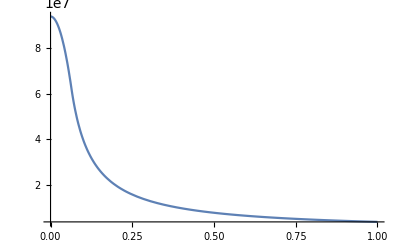

```mathematica
Plot[-Vgrav[r],{r,0,10^8},PlotRange->All]
```

```mathematica
-Vgrav[10^8]
```

3.98199×10^6

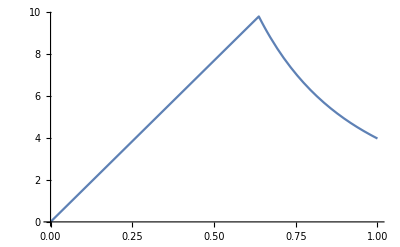

```mathematica
Plot[D[Vgrav[r],r]/.r->rt/.SIConstRepl/.EarthRepl,{rt,0,10^7}]
```

```mathematica
-D[Vgrav[r],r]
```

-(Piecewise[{{1.53985×10^-6 r, r<6371000}, {(3.98199×10^14)/r^2, r>6371000}, {Indeterminate, True}}])

#### Computed Cross-Sections

```mathematica
FeλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["FeλeDictSIOscillator_``",i]]],{i,6}];
```

```mathematica
(*Clear[FenesOscillator,FeσsOscillator]
FenesOscillator= Table[("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{i,Length[FeλeDictOscillators]}]
FeσsOscillator=Table[(10^(FeλeDictOscillators[[i]][["f"]][#1,#2])/FenesOscillator[[i]]),{i,Length[FeλeDictOscillators]}]*)
```

```mathematica
Show[Table[LogLogPlot[(FeλeDictOscillators[[i]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl},PlotRange->{10^-42,10^-27},PlotLabels->ToString[StringForm["``",i]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}],{i,Length[FeλeDictOscillators]}]]
Print["From this plot we see that as expected, the outer electron shells dominate the cross-section for Iron"]
```

-Graphics-

From this plot we see that as expected, the outer electron shells dominate the cross-section for Iron

Show the same plots as above, but with only one oscillator each to show the profile

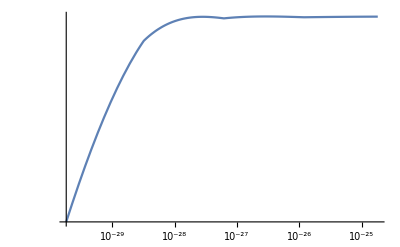

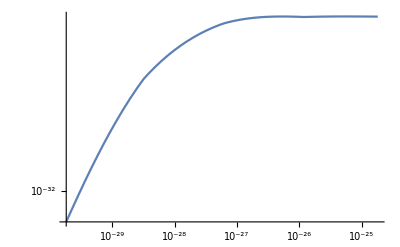

```mathematica
Print["Show the same plots as above, but with only one oscillator each to show the profile"]
LogLogPlot[(FeλeDictOscillators[[1]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[1]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl}]
LogLogPlot[(FeλeDictOscillators[[5]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[5]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl}]
```

```mathematica
Print["Extend the range of masses"]
Show[Table[LogLogPlot[(FeλeDictOscillators[[i]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{mχ,10^-32.3, 10^-23.4},PlotRange->{10^-42,10^-27},PlotLabels->ToString[StringForm["``",i]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}],{i,Length[FeλeDictOscillators]}]]
Print["Why are some of the oscillators being truncated at the same value of the mass? I would have guessed it would be the energy truncation we did, but because oscillator 4 is untruncated, this seems unlikely. So lets look at the values ω_(edge, i) where they were truncated at"]
"ωedgei"/.Table[FeλeDictOscillators[[i]][["fitparams"]][[1]],{i,Length[FeλeDictOscillators]}]
Print["And also the number densities"]
"ne"/.Table[FeλeDictOscillators[[i]][["fitparams"]][[1]],{i,Length[FeλeDictOscillators]}]
```

Extend the range of masses

-Graphics-

Why are some of the oscillators being truncated at the same value of the mass? I would have guessed it would be the energy truncation we did, but because oscillator 4 is untruncated, this seems unlikely. So lets look at the values ω_(edge, i) where they were truncated at

{6.04519×10^14,6.5887×10^12,3.02977×10^14,1.51848×10^14,1.09042×10^18,1.09893×10^19}

And also the number densities

{1.038×10^29,1.91532×10^29,4.34359×10^29,3.17873×10^30,4.14995×10^32,4.0004×10^34}

```mathematica
LogLogPlot[(FeλeDictOscillators[[3]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[3]][["fitparams"]][[1]]),{mχ,10^-32.3, 10^-23.4},PlotLabels->ToString[StringForm["``",3]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}]
```

-Graphics-

#### Recoil Energy Sampling

```mathematica
FeλeDictOscillators[[1]][["fitparams"]][[1]]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→2.49694×10^20,βcore→1.32379×10^19,SiO2Frac→0.447,MgOFrac→0.387|>

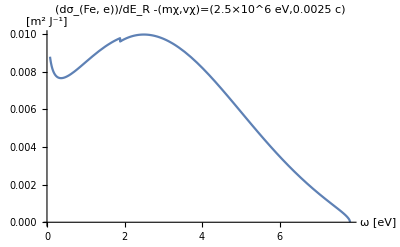

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[1]][["fitparams"]],βcore],{ω,10^-2 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

Now include the truncation due to the cutoff of available data

1.18632×10^16

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000310856}. NIntegrate obtained 0.0000421186 and 6.94605×10^-7 for the integral and error estimates.

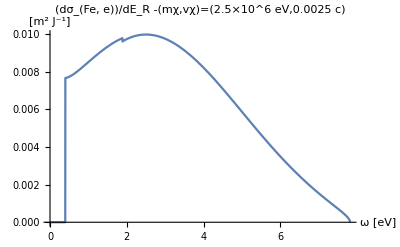

Notice that this is a cutoff sub eV

```mathematica
Print["Now include the truncation due to the cutoff of available data"]
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ERmaxtemp];
Print[Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[1]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[1]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]]
]
Print["Notice that this is a cutoff sub eV"]
```

Lets look at the outermost shell

1.18632×10^16

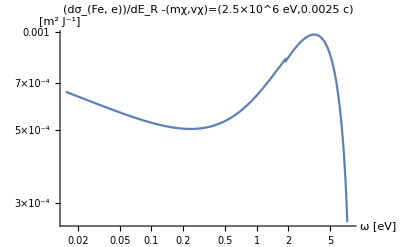

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00010936}. NIntegrate obtained 4.91141×10^-6 and 1.73417×10^-7 for the integral and error estimates.

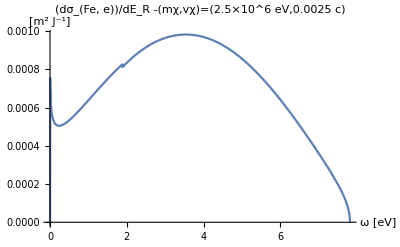

Notice this has a much lower cutoff

```mathematica
Print["Lets look at the outermost shell"]
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ERmaxtemp];
Print[LogLogPlot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[2]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[2]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Print[Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[2]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[2]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]]
]
Print["Notice this has a much lower cutoff"]
```

```mathematica
Testdσfunc[["dσTable"]][[;;,1]](("JpereV")/("ℏ"))^-1/.SIConstRepl
```

{0.004339,0.00620024,0.00885988,0.0126604,0.0180911,0.0258515,0.0369406,0.0527865,0.0754297,0.107786,0.154021,0.22009,0.314498,0.449405,0.64218,0.917647,1.31128,1.87376,2.67752,3.82606}

To interpolate, we need to determine the range over which to interpolate, and then evaluate the function at the points in a list, then interpolate

For the range: we want to evaluate from ω_(edge,i), then have some set number of evaluations, then we can do the interpolation

we also want to do this for each oscillator.

```mathematica
Testdσfunc=Block[{mχ,vχ,params,ERmin,ERmax,InterPω,n=20,InterdσTable,Interdσf},
(*Input parameters*)
mχ = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχ = 2.5 10^-3 "c"/.SIConstRepl;
params = FeλeDictOscillators[[2]][["fitparams"]][[1]];

(*local parameters*)
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];

Print[dσdERe[ERmax,mχ,vχ,{params},"β"/.params]];
Print[ERmax];
Print[InterPω[[n+1]]];
Print[ERmax==InterPω[[n+1]]];
Print[dσdERe[N[InterPω[[n+1]](1-10^-3)],mχ,vχ,{params},"β"/.params]];

InterdσTable=Table[{InterPω[[i]],dσdERe[InterPω[[i]](1-10^-3),mχ,vχ,{params},"β"/.params]HeavisideTheta[InterPω[[i]]-ERmin]},{i,n+1}];
Interdσf=Interpolation[InterdσTable];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->InterPω|>
]
```

0.

1.18632×10^16

1.18632×10^16

True

0.0000287166

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003463745696036182202849629252483509844751097261905670166015625}. NIntegrate obtained 0.000113854 and 6.1034×10^-9 for the integral and error estimates.

<|dσf→InterpolatingFunction[…],dσTable→{{6.5887×10^12,0.000763026},{9.58451×10^12,0.000730472},{1.39425×10^13,0.000698427},{2.0282×10^13,0.000667086},{2.95039×10^13,0.000636717},{4.2919×10^13,0.000607674},{6.24338×10^13,0.000580439},{9.08217×10^13,0.00055567},{1.32117×10^14,0.000534269},{1.9219×10^14,0.000517488},{2.79576×10^14,0.000507088},{4.06696×10^14,0.000505583},{5.91616×10^14,0.000516596},{8.60617×10^14,0.000545281},{1.25193×10^15,0.000598449},{1.82117×10^15,0.000683001},{2.64923×10^15,0.00079926},{3.85381×10^15,0.000919998},{5.60609×10^15,0.000980598},{8.15511×10^15,0.000787263},{1.18632×10^16,0.0000287166}},Interpoints→{6.5887×10^12,9.58451×10^12,1.39425×10^13,2.0282×10^13,2.95039×10^13,4.2919×10^13,6.24338×10^13,9.08217×10^13,1.32117×10^14,1.9219×10^14,2.79576×10^14,4.06696×10^14,5.91616×10^14,8.60617×10^14,1.25193×10^15,1.82117×10^15,2.64923×10^15,3.85381×10^15,5.60609×10^15,8.15511×10^15,1.18632×10^16}|>

```mathematica
InterpolatedσdERe[mχ_,vχ_,params_]:=Module[{ERmin,ERmax,InterPω,ϵ,n=20,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)
(*local parameters*)
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];
ϵ=10^-10;(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)

InterdσTable=Table[{InterPω[[i]],dσdERe[InterPω[[i]](1-ϵ),mχ,vχ,{params},"β"/.params]HeavisideTheta[InterPω[[i]]-ERmin]},{i,n+1}];
Interdσf=Interpolation[InterdσTable];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->InterPω|>
]
```

```mathematica
InterpolatedσdERe2 =InterpolatedσdERe[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl, FeλeDictOscillators[[2]][["fitparams"]][[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0002782473013753506880271597345721801275431062094867229461669921875}. NIntegrate obtained 0.000113954 and 6.13129×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000602666718839405825790256354679286232567392289638519287109375}. NIntegrate obtained 0.000158367 and 1.4707×10^-9 for the integral and error estimates.

<|dσf→InterpolatingFunction[…],dσTable→{{6.5887×10^12,0.000762938},{9.58451×10^12,0.000730402},{1.39425×10^13,0.000698342},{2.0282×10^13,0.000667004},{2.95039×10^13,0.000636637},{4.2919×10^13,0.000607598},{6.24338×10^13,0.000580369},{9.08217×10^13,0.000555607},{1.32117×10^14,0.000534217},{1.9219×10^14,0.000517451},{2.79576×10^14,0.000507071},{4.06696×10^14,0.000505594},{5.91616×10^14,0.000516646},{8.60617×10^14,0.000545387},{1.25193×10^15,0.00059863},{1.82117×10^15,0.000683272},{2.64923×10^15,0.000799601},{3.85381×10^15,0.000920314},{5.60609×10^15,0.000980529},{8.15511×10^15,0.000786165},{1.18632×10^16,9.05968×10^-9}},Interpoints→{6.5887×10^12,9.58451×10^12,1.39425×10^13,2.0282×10^13,2.95039×10^13,4.2919×10^13,6.24338×10^13,9.08217×10^13,1.32117×10^14,1.9219×10^14,2.79576×10^14,4.06696×10^14,5.91616×10^14,8.60617×10^14,1.25193×10^15,1.82117×10^15,2.64923×10^15,3.85381×10^15,5.60609×10^15,8.15511×10^15,1.18632×10^16}|>

```mathematica
Print["Show the Block which we've tested, and the module we have written give the same expression"]
Plot[Testdσfunc[["dσf"]][ω],{ω,Testdσfunc[["Interpoints"]][[1]],Testdσfunc[["Interpoints"]][[-1]]}]
Plot[InterpolatedσdERe2 [["dσf"]][ω],{ω,InterpolatedσdERe2 [["Interpoints"]][[1]],InterpolatedσdERe2 [["Interpoints"]][[-1]]}]
```

Show the Block which we've tested, and the module we have written give the same expression

-Graphics-

-Graphics-

```mathematica
NIntegrate[Testdσfunc[["dσf"]][ω],{ω,Testdσfunc[["Interpoints"]][[1]],Testdσfunc[["Interpoints"]][[-1]]}]
```

8.37856×10^12

#### Interpolate over vχ as well as ω

```mathematica
GetvχandωList[mχ_,vχ_,params_,n_:20]:=Module[{ERmin,ERmax,ϵ,Interpointsω},
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;

Interpointsω=10^Subdivide[Log10[ERmin],Log10[ERmax],n];
Table[{vχ,Interpointsω[[i]]},{i,n+1}]
]
```

```mathematica
GetvχandωList[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]]]
```

{{750000.,6.5887×10^12},{750000.,9.58451×10^12},{750000.,1.39425×10^13},{750000.,2.0282×10^13},{750000.,2.95039×10^13},{750000.,4.2919×10^13},{750000.,6.24338×10^13},{750000.,9.08217×10^13},{750000.,1.32117×10^14},{750000.,1.9219×10^14},{750000.,2.79576×10^14},{750000.,4.06696×10^14},{750000.,5.91616×10^14},{750000.,8.60617×10^14},{750000.,1.25193×10^15},{750000.,1.82117×10^15},{750000.,2.64923×10^15},{750000.,3.85381×10^15},{750000.,5.60609×10^15},{750000.,8.15511×10^15}}

```mathematica
InterpolatvχandωσdERe[mχ_,vχ_:{10^-5,10^-2}"c"/.SIConstRepl,params_,m_:4,n_:20]:=Module[{ωmin,Interpointsvχ,Interpointsvχandω,ϵ,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*local parameters*)
(*ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];*)
ωmin= "ωedgei"/.params;
Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Interpointsvχandω=SortBy[Table[GetvχandωList[mχ,Interpointsvχ[[i]],params,n],{i,m+1}],Last];
ϵ=10^-4;(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)
(*Print[Interpointsvχandω[[1,1]][[1]]];
Print[Interpointsvχandω[[1,1]][[2]]];*)
(*Print[dσdERe[6.588699526066354*^12(1+ϵ),mχ,3000(1+ϵ),{params},"β"/.params]];
Print[dσdERe[Interpointsvχandω[[1,1]][[2]](1+ϵ),mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]];*)
InterdσTable=Table[{Interpointsvχandω[[i,j]],dσdERe[Interpointsvχandω[[i,j]][[2]],mχ,Interpointsvχandω[[i,j]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[i,j]][[2]]-ωmin]},{i,m+1},{j,n+1}];
Interdσf=Interpolation[Flatten[Log10[InterdσTable],1]];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandω,"Interpointsvχ"->Interpointsvχ|>
]
```

```mathematica
testkinσinterpolate=InterpolatvχandωσdERe[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],4,20]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000125028}. NIntegrate obtained 0.000128098 and 1.87966×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00023053}. NIntegrate obtained 0.000210627 and 6.68139×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00019964873741304990040971827081062173192549380473792552947998046875}. NIntegrate obtained 0.000331927 and 4.00527×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

<|dσf→InterpolatingFunction[…],dσTable→{{{{30000,6.5887×10^12},0.128779},{{30000,6.94665×10^12},0.125043},{{30000,7.32406×10^12},0.121248},{{30000,7.72196×10^12},0.117387},{{30000,8.14149×10^12},0.113453},{{30000,8.5838×10^12},0.109437},{{30000,9.05015×10^12},0.10533},{{30000,9.54183×10^12},0.101119},{{30000,1.00602×10^13},0.0967902},{{30000,1.06068×10^13},0.0923255},{{30000,1.1183×10^13},0.0877034},{{30000,1.17906×10^13},0.0828965},{{30000,1.24312×10^13},0.0778694},{{30000,1.31065×10^13},0.0725748},{{30000,1.38186×10^13},0.066948},{{30000,1.45693×10^13},0.060895},{{30000,1.53609×10^13},0.0542717},{{30000,1.61954×10^13},0.0468342},{{30000,1.70753×10^13},0.0381056},{{30000,1.8003×10^13},0.0268509},{{30000,1.8981×10^13},1.16337×10^-6}},{{{300000,6.5887×10^12},0.00414931},{{300000,8.74532×10^12},0.00399408},{{300000,1.16078×10^13},0.00384017},{{300000,1.54073×10^13},0.00368792},{{300000,2.04505×10^13},0.00353772},{{300000,2.71444×10^13},0.00339007},{{300000,3.60293×10^13},0.00324558},{{300000,4.78225×10^13},0.00310498},{{300000,6.34758×10^13},0.00296914},{{300000,8.42527×10^13},0.00283909},{{300000,1.1183×10^14},0.00271602},{{300000,1.48435×10^14},0.00260126},{{300000,1.97021×10^14},0.00249623},{{300000,2.6151×10^14},0.00240224},{{300000,3.47107×10^14},0.00232005},{{300000,4.60723×10^14},0.00224882},{{300000,6.11528×10^14},0.00218355},{{300000,8.11693×10^14},0.00210868},{{300000,1.07738×10^15},0.00198043},{{300000,1.43003×10^15},0.00166523},{{300000,1.8981×10^15},3.83751×10^-8}},{{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000529074},{{3000000,1.83972×10^13},0.0000501535},{{3000000,3.07417×10^13},0.0000476051},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},2.65079×10^-14}},{{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,7.79427×10^12},0.0269579},{{30000 √10,9.22044×10^12},0.0260032},{{30000 √10,1.09076×10^13},0.0250463},{{30000 √10,1.29034×10^13},0.0240866},{{30000 √10,1.52644×10^13},0.0231232},{{30000 √10,1.80574×10^13},0.0221549},{{30000 √10,2.13615×10^13},0.0211802},{{30000 √10,2.52702×10^13},0.0201969},{{30000 √10,2.9894×10^13},0.0192024},{{30000 √10,3.53639×10^13},0.018193},{{30000 √10,4.18346×10^13},0.0171637},{{30000 √10,4.94894×10^13},0.0161076},{{30000 √10,5.85447×10^13},0.0150151},{{30000 √10,6.9257×10^13},0.0138721},{{30000 √10,8.19294×10^13},0.0126577},{{30000 √10,9.69206×10^13},0.0113384},{{30000 √10,1.14655×10^14},0.00985722},{{30000 √10,1.35634×10^14},0.00810197},{{30000 √10,1.60452×10^14},0.00578626},{{30000 √10,1.8981×10^14},1.43132×10^-7}},{{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,9.81241×10^12},0.000468611},{{300000 √10,1.46134×10^13},0.000447422},{{300000 √10,2.17635×10^13},0.000426766},{{300000 √10,3.24118×10^13},0.000406875},{{300000 √10,4.82703×10^13},0.00038805},{{300000 √10,7.18879×10^13},0.000370713},{{300000 √10,1.07061×10^14},0.00035546},{{300000 √10,1.59444×10^14},0.000343132},{{300000 √10,2.37456×10^14},0.000334941},{{300000 √10,3.53639×10^14},0.000332674},{{300000 √10,5.26667×10^14},0.000339008},{{300000 √10,7.84354×10^14},0.000358055},{{300000 √10,1.16812×10^15},0.000395656},{{300000 √10,1.73966×10^15},0.000459763},{{300000 √10,2.59084×10^15},0.000556967},{{300000 √10,3.85848×10^15},0.000680416},{{300000 √10,5.74635×10^15},0.00080825},{{300000 √10,8.55792×10^15},0.000829791},{{300000 √10,1.27451×10^16},0.000502176},{{300000 √10,1.8981×10^16},2.26382×10^-9}}},Interpoints→{{{30000,6.5887×10^12},{30000,6.94665×10^12},{30000,7.32406×10^12},{30000,7.72196×10^12},{30000,8.14149×10^12},{30000,8.5838×10^12},{30000,9.05015×10^12},{30000,9.54183×10^12},{30000,1.00602×10^13},{30000,1.06068×10^13},{30000,1.1183×10^13},{30000,1.17906×10^13},{30000,1.24312×10^13},{30000,1.31065×10^13},{30000,1.38186×10^13},{30000,1.45693×10^13},{30000,1.53609×10^13},{30000,1.61954×10^13},{30000,1.70753×10^13},{30000,1.8003×10^13},{30000,1.8981×10^13}},{{300000,6.5887×10^12},{300000,8.74532×10^12},{300000,1.16078×10^13},{300000,1.54073×10^13},{300000,2.04505×10^13},{300000,2.71444×10^13},{300000,3.60293×10^13},{300000,4.78225×10^13},{300000,6.34758×10^13},{300000,8.42527×10^13},{300000,1.1183×10^14},{300000,1.48435×10^14},{300000,1.97021×10^14},{300000,2.6151×10^14},{300000,3.47107×10^14},{300000,4.60723×10^14},{300000,6.11528×10^14},{300000,8.11693×10^14},{300000,1.07738×10^15},{300000,1.43003×10^15},{300000,1.8981×10^15}},{{3000000,6.5887×10^12},{3000000,1.10097×10^13},{3000000,1.83972×10^13},{3000000,3.07417×10^13},{3000000,5.13693×10^13},{3000000,8.5838×10^13},{3000000,1.43435×10^14},{3000000,2.3968×10^14},{3000000,4.00505×10^14},{3000000,6.69243×10^14},{3000000,1.1183×10^15},{3000000,1.86868×10^15},{3000000,3.12257×10^15},{3000000,5.21781×10^15},{3000000,8.71895×10^15},{3000000,1.45693×10^16},{3000000,2.43453×10^16},{3000000,4.0681×10^16},{3000000,6.79779×10^16},{3000000,1.13591×10^17},{3000000,1.8981×10^17}},{{30000 √10,6.5887×10^12},{30000 √10,7.79427×10^12},{30000 √10,9.22044×10^12},{30000 √10,1.09076×10^13},{30000 √10,1.29034×10^13},{30000 √10,1.52644×10^13},{30000 √10,1.80574×10^13},{30000 √10,2.13615×10^13},{30000 √10,2.52702×10^13},{30000 √10,2.9894×10^13},{30000 √10,3.53639×10^13},{30000 √10,4.18346×10^13},{30000 √10,4.94894×10^13},{30000 √10,5.85447×10^13},{30000 √10,6.9257×10^13},{30000 √10,8.19294×10^13},{30000 √10,9.69206×10^13},{30000 √10,1.14655×10^14},{30000 √10,1.35634×10^14},{30000 √10,1.60452×10^14},{30000 √10,1.8981×10^14}},{{300000 √10,6.5887×10^12},{300000 √10,9.81241×10^12},{300000 √10,1.46134×10^13},{300000 √10,2.17635×10^13},{300000 √10,3.24118×10^13},{300000 √10,4.82703×10^13},{300000 √10,7.18879×10^13},{300000 √10,1.07061×10^14},{300000 √10,1.59444×10^14},{300000 √10,2.37456×10^14},{300000 √10,3.53639×10^14},{300000 √10,5.26667×10^14},{300000 √10,7.84354×10^14},{300000 √10,1.16812×10^15},{300000 √10,1.73966×10^15},{300000 √10,2.59084×10^15},{300000 √10,3.85848×10^15},{300000 √10,5.74635×10^15},{300000 √10,8.55792×10^15},{300000 √10,1.27451×10^16},{300000 √10,1.8981×10^16}}},Interpointsvχ→{30000,30000 √10,300000,300000 √10,3000000}|>

```mathematica
testkinσinterpolate[["dσf"]][5,13]
```

Missing[KeyAbsent,5]

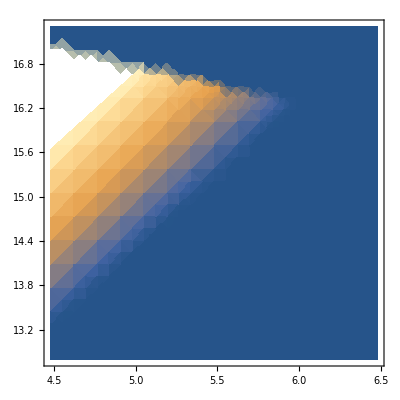

```mathematica
DensityPlot[testkinσinterpolate[["dσf"]][vχ,ω],{vχ,4.48,6.48},{ω,12.8,17.3}]
```

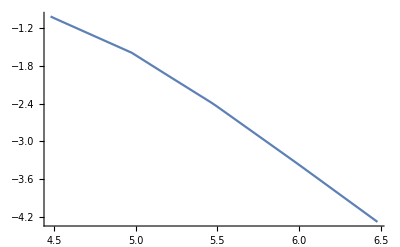

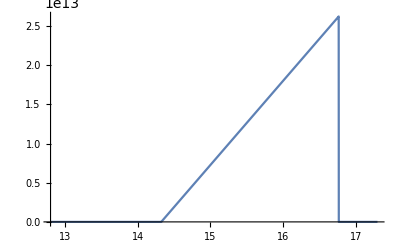

Because the grid of ω and vχ is unstructured, we get a simple linear fit. Try taking the max ωmax in the grid and just cutting off with a heaviside

```mathematica
Plot[testkinσinterpolate[["dσf"]][vχ,13],{vχ,4.48,6.48}]
Plot[testkinσinterpolate[["dσf"]][5,ω],{ω,12.8,17.3}]
Print["Because the grid of ω and vχ is unstructured, we get a simple linear fit. Try taking the max ωmax in the grid and just cutting off with a heaviside"]
```

#### Try interpolating over vχ and ω, but with a square grid

```mathematica
GetvχandωListSquare[mχ_,vχ_,ωmax_,params_,n_:20]:=Module[{ωmin,ϵ,Interpointsω},
ωmin= "ωedgei"/.params;
(*ERmax = ωmax;*)

Interpointsω=10^Subdivide[Log10[ωmin],Log10[ωmax],n];
Table[{vχ,Interpointsω[[i]]},{i,n+1}]
]
```

```mathematica
InterpolatvχandωσdEReSquare[mχ_,vχ_:{10^-5,10^-2}"c"/.SIConstRepl,params_,m_:4,n_:20]:=Module[{ωmin,ωmax,Interpointsvχ,Interpointsvχandω,ϵ,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*local parameters*)
(*ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];*)
ωmin= "ωedgei"/.params;
ωmax =  1/(2"ℏ")mχ vχ[[2]]^2/.params;
Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Print[GetvχandωListSquare[mχ,Interpointsvχ[[1]],ωmax,params,n]];
Interpointsvχandω=Table[GetvχandωListSquare[mχ,Interpointsvχ[[i]],ωmax,params,n],{i,m+1}];
(*Interpointsvχandω=Table[GetvχandωListSquare[mχ,Interpointsvχ[[i]],ωmax,params,n],{i,m+1}];*)
(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)
(*Print[Interpointsvχandω[[1,1]][[1]]];
Print[Interpointsvχandω[[1,1]][[2]]];*)
(*Print[dσdERe[6.588699526066354*^12(1+ϵ),mχ,3000(1+ϵ),{params},"β"/.params]];
Print[dσdERe[Interpointsvχandω[[1,1]][[2]](1+ϵ),mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]];*)
Print[dσdERe[Interpointsvχandω[[1,1]][[2]],mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[1,1]][[2]]-ωmin]HeavisideTheta[( mχ/(2"ℏ")(Interpointsvχandω[[1,1]][[1]])^2/.params)-Interpointsvχandω[[1,1]][[2]]]];
InterdσTable=Table[{Interpointsvχandω[[i,j]],dσdERe[Interpointsvχandω[[i,j]][[2]],mχ,Interpointsvχandω[[i,j]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[i,j]][[2]]-ωmin]HeavisideTheta[( mχ/(2"ℏ")(Interpointsvχandω[[i,j]][[1]])^2/.params)-Interpointsvχandω[[i,j]][[2]]]},{i,m+1},{j,n+1}];
Print[Flatten[InterdσTable,1]];
Interdσf=Interpolation[Flatten[InterdσTable,1]];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandω,"Interpointsvχ"->Interpointsvχ|>
]
```

```mathematica
testkinσinterpolateSquare=InterpolatvχandωσdEReSquare[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],4,20]
```

{{30000,6.5887×10^12},{30000,1.10097×10^13},{30000,1.83972×10^13},{30000,3.07417×10^13},{30000,5.13693×10^13},{30000,8.5838×10^13},{30000,1.43435×10^14},{30000,2.3968×10^14},{30000,4.00505×10^14},{30000,6.69243×10^14},{30000,1.1183×10^15},{30000,1.86868×10^15},{30000,3.12257×10^15},{30000,5.21781×10^15},{30000,8.71895×10^15},{30000,1.45693×10^16},{30000,2.43453×10^16},{30000,4.0681×10^16},{30000,6.79779×10^16},{30000,1.13591×10^17},{30000,1.8981×10^17}}

0.128779

NIntegrate::inumr: The integrand -(0.0699144 Im[1/ϵMNum[0.000834741/(EnergyLoss`Private`z),EnergyLoss`Private`z,(«20»)/(«20»),{«1»}]])/(EnergyLoss`Private`z) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.0354795-0.0279276 ⅈ,0.0354795+0. ⅈ}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00032159492022796235086330718377922721629147417843341827392578125}. NIntegrate obtained 0.000117156 and 2.2645×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003657868553803155195242209629657992309148539789021015167236328125}. NIntegrate obtained 0.000184102 and 1.80922×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.12196132850382213064222014509141445159912109375-0.54156685354676916268642291229238270738745584159086009742098706683 ⅈ}. NIntegrate obtained -0.000636687+0.00105807 ⅈ and 1.24195×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{{30000,6.5887×10^12},0.128779},{{30000,1.10097×10^13},0.0890861},{{30000,1.83972×10^13},0.0206049},{{30000,3.07417×10^13},0.},{{30000,5.13693×10^13},0.},{{30000,8.5838×10^13},0.},{{30000,1.43435×10^14},0.},{{30000,2.3968×10^14},0.},{{30000,4.00505×10^14},0.},{{30000,6.69243×10^14},0.},{{30000,1.1183×10^15},0.},{{30000,1.86868×10^15},0.},{{30000,3.12257×10^15},0.},{{30000,5.21781×10^15},0.},{{30000,8.71895×10^15},0.},{{30000,1.45693×10^16},0.},{{30000,2.43453×10^16},0.},{{30000,4.0681×10^16},0.},{{30000,6.79779×10^16},0.},{{30000,1.13591×10^17},0.},{{30000,1.8981×10^17},0.},{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,1.10097×10^13},0.0249931},{{30000 √10,1.83972×10^13},0.0220471},{{30000 √10,3.07417×10^13},0.0190356},{{30000 √10,5.13693×10^13},0.0158688},{{30000 √10,8.5838×10^13},0.0123041},{{30000 √10,1.43435×10^14},0.00741879},{{30000 √10,2.3968×10^14},0.},{{30000 √10,4.00505×10^14},0.},{{30000 √10,6.69243×10^14},0.},{{30000 √10,1.1183×10^15},0.},{{30000 √10,1.86868×10^15},0.},{{30000 √10,3.12257×10^15},0.},{{30000 √10,5.21781×10^15},0.},{{30000 √10,8.71895×10^15},0.},{{30000 √10,1.45693×10^16},0.},{{30000 √10,2.43453×10^16},0.},{{30000 √10,4.0681×10^16},0.},{{30000 √10,6.79779×10^16},0.},{{30000 √10,1.13591×10^17},0.},{{30000 √10,1.8981×10^17},0.},{{300000,6.5887×10^12},0.00414931},{{300000,1.10097×10^13},0.00386881},{{300000,1.83972×10^13},0.00359357},{{300000,3.07417×10^13},0.00332614},{{300000,5.13693×10^13},0.00307017},{{300000,8.5838×10^13},0.00283076},{{300000,1.43435×10^14},0.00261466},{{300000,2.3968×10^14},0.00242994},{{300000,4.00505×10^14},0.00228286},{{300000,6.69243×10^14},0.002162},{{300000,1.1183×10^15},0.00195456},{{300000,1.86868×10^15},0.000473946},{{300000,3.12257×10^15},0.},{{300000,5.21781×10^15},0.},{{300000,8.71895×10^15},0.},{{300000,1.45693×10^16},0.},{{300000,2.43453×10^16},0.},{{300000,4.0681×10^16},0.},{{300000,6.79779×10^16},0.},{{300000,1.13591×10^17},0.},{{300000,1.8981×10^17},0.},{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,1.10097×10^13},0.000462445},{{300000 √10,1.83972×10^13},0.000435401},{{300000 √10,3.07417×10^13},0.000409463},{{300000 √10,5.13693×10^13},0.00038523},{{300000 √10,8.5838×10^13},0.000363621},{{300000 √10,1.43435×10^14},0.000346061},{{300000 √10,2.3968×10^14},0.000334812},{{300000 √10,4.00505×10^14},0.000333572},{{300000 √10,6.69243×10^14},0.000348584},{{300000 √10,1.1183×10^15},0.000390397},{{300000 √10,1.86868×10^15},0.000474681},{{300000 √10,3.12257×10^15},0.000605796},{{300000 √10,5.21781×10^15},0.000781326},{{300000 √10,8.71895×10^15},0.000824436},{{300000 √10,1.45693×10^16},0.000319572},{{300000 √10,2.43453×10^16},0.+0. ⅈ},{{300000 √10,4.0681×10^16},0.+0. ⅈ},{{300000 √10,6.79779×10^16},0.+0. ⅈ},{{300000 √10,1.13591×10^17},0.+0. ⅈ},{{300000 √10,1.8981×10^17},0.+0. ⅈ},{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000530238},{{3000000,1.83972×10^13},0.0000501318},{{3000000,3.07417×10^13},0.0000476047},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},0.+0. ⅈ}}

<|dσf→InterpolatingFunction[…],dσTable→{{{{30000,6.5887×10^12},0.128779},{{30000,1.10097×10^13},0.0890861},{{30000,1.83972×10^13},0.0206049},{{30000,3.07417×10^13},0.},{{30000,5.13693×10^13},0.},{{30000,8.5838×10^13},0.},{{30000,1.43435×10^14},0.},{{30000,2.3968×10^14},0.},{{30000,4.00505×10^14},0.},{{30000,6.69243×10^14},0.},{{30000,1.1183×10^15},0.},{{30000,1.86868×10^15},0.},{{30000,3.12257×10^15},0.},{{30000,5.21781×10^15},0.},{{30000,8.71895×10^15},0.},{{30000,1.45693×10^16},0.},{{30000,2.43453×10^16},0.},{{30000,4.0681×10^16},0.},{{30000,6.79779×10^16},0.},{{30000,1.13591×10^17},0.},{{30000,1.8981×10^17},0.}},{{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,1.10097×10^13},0.0249931},{{30000 √10,1.83972×10^13},0.0220471},{{30000 √10,3.07417×10^13},0.0190356},{{30000 √10,5.13693×10^13},0.0158688},{{30000 √10,8.5838×10^13},0.0123041},{{30000 √10,1.43435×10^14},0.00741879},{{30000 √10,2.3968×10^14},0.},{{30000 √10,4.00505×10^14},0.},{{30000 √10,6.69243×10^14},0.},{{30000 √10,1.1183×10^15},0.},{{30000 √10,1.86868×10^15},0.},{{30000 √10,3.12257×10^15},0.},{{30000 √10,5.21781×10^15},0.},{{30000 √10,8.71895×10^15},0.},{{30000 √10,1.45693×10^16},0.},{{30000 √10,2.43453×10^16},0.},{{30000 √10,4.0681×10^16},0.},{{30000 √10,6.79779×10^16},0.},{{30000 √10,1.13591×10^17},0.},{{30000 √10,1.8981×10^17},0.}},{{{300000,6.5887×10^12},0.00414931},{{300000,1.10097×10^13},0.00386881},{{300000,1.83972×10^13},0.00359357},{{300000,3.07417×10^13},0.00332614},{{300000,5.13693×10^13},0.00307017},{{300000,8.5838×10^13},0.00283076},{{300000,1.43435×10^14},0.00261466},{{300000,2.3968×10^14},0.00242994},{{300000,4.00505×10^14},0.00228286},{{300000,6.69243×10^14},0.002162},{{300000,1.1183×10^15},0.00195456},{{300000,1.86868×10^15},0.000473946},{{300000,3.12257×10^15},0.},{{300000,5.21781×10^15},0.},{{300000,8.71895×10^15},0.},{{300000,1.45693×10^16},0.},{{300000,2.43453×10^16},0.},{{300000,4.0681×10^16},0.},{{300000,6.79779×10^16},0.},{{300000,1.13591×10^17},0.},{{300000,1.8981×10^17},0.}},{{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,1.10097×10^13},0.000462445},{{300000 √10,1.83972×10^13},0.000435401},{{300000 √10,3.07417×10^13},0.000409463},{{300000 √10,5.13693×10^13},0.00038523},{{300000 √10,8.5838×10^13},0.000363621},{{300000 √10,1.43435×10^14},0.000346061},{{300000 √10,2.3968×10^14},0.000334812},{{300000 √10,4.00505×10^14},0.000333572},{{300000 √10,6.69243×10^14},0.000348584},{{300000 √10,1.1183×10^15},0.000390397},{{300000 √10,1.86868×10^15},0.000474681},{{300000 √10,3.12257×10^15},0.000605796},{{300000 √10,5.21781×10^15},0.000781326},{{300000 √10,8.71895×10^15},0.000824436},{{300000 √10,1.45693×10^16},0.000319572},{{300000 √10,2.43453×10^16},0.+0. ⅈ},{{300000 √10,4.0681×10^16},0.+0. ⅈ},{{300000 √10,6.79779×10^16},0.+0. ⅈ},{{300000 √10,1.13591×10^17},0.+0. ⅈ},{{300000 √10,1.8981×10^17},0.+0. ⅈ}},{{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000530238},{{3000000,1.83972×10^13},0.0000501318},{{3000000,3.07417×10^13},0.0000476047},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},0.+0. ⅈ}}},Interpoints→{{{30000,6.5887×10^12},{30000,1.10097×10^13},{30000,1.83972×10^13},{30000,3.07417×10^13},{30000,5.13693×10^13},{30000,8.5838×10^13},{30000,1.43435×10^14},{30000,2.3968×10^14},{30000,4.00505×10^14},{30000,6.69243×10^14},{30000,1.1183×10^15},{30000,1.86868×10^15},{30000,3.12257×10^15},{30000,5.21781×10^15},{30000,8.71895×10^15},{30000,1.45693×10^16},{30000,2.43453×10^16},{30000,4.0681×10^16},{30000,6.79779×10^16},{30000,1.13591×10^17},{30000,1.8981×10^17}},{{30000 √10,6.5887×10^12},{30000 √10,1.10097×10^13},{30000 √10,1.83972×10^13},{30000 √10,3.07417×10^13},{30000 √10,5.13693×10^13},{30000 √10,8.5838×10^13},{30000 √10,1.43435×10^14},{30000 √10,2.3968×10^14},{30000 √10,4.00505×10^14},{30000 √10,6.69243×10^14},{30000 √10,1.1183×10^15},{30000 √10,1.86868×10^15},{30000 √10,3.12257×10^15},{30000 √10,5.21781×10^15},{30000 √10,8.71895×10^15},{30000 √10,1.45693×10^16},{30000 √10,2.43453×10^16},{30000 √10,4.0681×10^16},{30000 √10,6.79779×10^16},{30000 √10,1.13591×10^17},{30000 √10,1.8981×10^17}},{{300000,6.5887×10^12},{300000,1.10097×10^13},{300000,1.83972×10^13},{300000,3.07417×10^13},{300000,5.13693×10^13},{300000,8.5838×10^13},{300000,1.43435×10^14},{300000,2.3968×10^14},{300000,4.00505×10^14},{300000,6.69243×10^14},{300000,1.1183×10^15},{300000,1.86868×10^15},{300000,3.12257×10^15},{300000,5.21781×10^15},{300000,8.71895×10^15},{300000,1.45693×10^16},{300000,2.43453×10^16},{300000,4.0681×10^16},{300000,6.79779×10^16},{300000,1.13591×10^17},{300000,1.8981×10^17}},{{300000 √10,6.5887×10^12},{300000 √10,1.10097×10^13},{300000 √10,1.83972×10^13},{300000 √10,3.07417×10^13},{300000 √10,5.13693×10^13},{300000 √10,8.5838×10^13},{300000 √10,1.43435×10^14},{300000 √10,2.3968×10^14},{300000 √10,4.00505×10^14},{300000 √10,6.69243×10^14},{300000 √10,1.1183×10^15},{300000 √10,1.86868×10^15},{300000 √10,3.12257×10^15},{300000 √10,5.21781×10^15},{300000 √10,8.71895×10^15},{300000 √10,1.45693×10^16},{300000 √10,2.43453×10^16},{300000 √10,4.0681×10^16},{300000 √10,6.79779×10^16},{300000 √10,1.13591×10^17},{300000 √10,1.8981×10^17}},{{3000000,6.5887×10^12},{3000000,1.10097×10^13},{3000000,1.83972×10^13},{3000000,3.07417×10^13},{3000000,5.13693×10^13},{3000000,8.5838×10^13},{3000000,1.43435×10^14},{3000000,2.3968×10^14},{3000000,4.00505×10^14},{3000000,6.69243×10^14},{3000000,1.1183×10^15},{3000000,1.86868×10^15},{3000000,3.12257×10^15},{3000000,5.21781×10^15},{3000000,8.71895×10^15},{3000000,1.45693×10^16},{3000000,2.43453×10^16},{3000000,4.0681×10^16},{3000000,6.79779×10^16},{3000000,1.13591×10^17},{3000000,1.8981×10^17}}},Interpointsvχ→{30000,30000 √10,300000,300000 √10,3000000}|>

InterpolatingFunction::dmval: Input value {4.48014,12.8003} lies outside the range of data in the interpolating function. Extrapolation will be used.

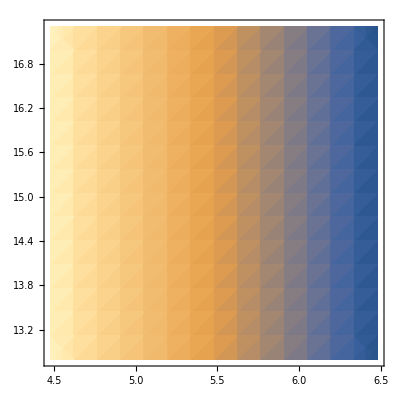

```mathematica
DensityPlot[testkinσinterpolateSquare[["dσf"]][vχ,ω],{vχ,4.48,6.48},{ω,12.8,17.3}]
```

InterpolatingFunction::dmval: Input value {4.48004,13} lies outside the range of data in the interpolating function. Extrapolation will be used.

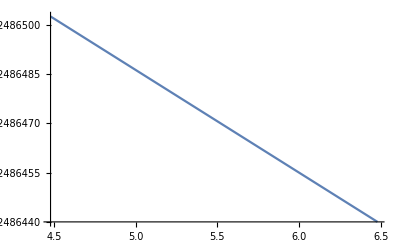

InterpolatingFunction::dmval: Input value {5,13.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

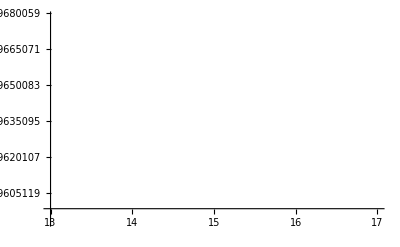

```mathematica
Plot[testkinσinterpolateSquare[["dσf"]][vχ,13],{vχ,4.48,6.48}]
Plot[testkinσinterpolateSquare[["dσf"]][5,ω],{ω,13,17}]
```

#### Interpolate with vχ and ξ

Psuedo-code:

We want to use ξ ∈ [0,1) with ω(ξ) = ω_min+ξ(ω_max-ω_min)
This should eleviate both issues we were having before, it interpolates only over the region of integration (so we get variation with ω and no issues with Heavisides) and also is a square grid (so no reduced order interpolations)

```mathematica
GetvχandξList[vχ_,n_:20,ϵ_:10^-4]:=Module[{Interpointsξ},
(*Interpointsξ=10^Subdivide[Log10[ϵ],Log10[1-ϵ],n];*)
Interpointsξ=Subdivide[ϵ,1-ϵ,n];(*move slightly away from the boundaries so we can do a log-log interpolation (dσ/Subscript[dE, R]->0 at Subscript[ω, max], and ξ->0 at Subscript[ω, min])*)
Table[{vχ,Interpointsξ[[i]]},{i,n+1}]
]
ωofξ[ξ_,ωmin_,ωmax_]:=ωmin + ξ (ωmax - ωmin)
ωmaxofvχ[vχ_,mχ_,params_]:= 1/(2"ℏ")mχ vχ^2/.params
ωofξandvχ[ξ_,ωmin_,vχ_,mχ_,params_]:=ωmin + ξ (ωmaxofvχ[vχ,mχ,params] - ωmin)
ξofωandvχ[ω_,ωmin_,vχ_,mχ_,params_]:=(ω-ωmin)/(ωmaxofvχ[vχ,mχ,params] - ωmin)
```

```mathematica
Clear[InterpolatevχandωσdEReξ]
InterpolatevχandωσdEReξ[mχ_,vχ_:{10^-5,10^-2}"c"/.SIConstRepl,params_,m_:4,n_:20,ϵ_:10^-4,cut_:4]:=Module[{ωmin,ωmax,Interpointsvχ,Interpointsvχandξ,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

ωmin= "ωedgei"/.params;

Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Interpointsvχandξ=SortBy[Table[GetvχandξList[Interpointsvχ[[i]],n,ϵ],{i,m+1}],Last];

InterdσTable=Table[{Interpointsvχandξ[[i,j]],dσdERe[ωofξ[Interpointsvχandξ[[i,j]][[2]],ωmin,ωmaxofvχ[Interpointsvχandξ[[i,j]][[1]],mχ,params]],mχ,Interpointsvχandξ[[i,j]][[1]],{params},"β"/.params,cut]},{i,m+1},{j,n+1}];
Interdσf=Interpolation[Flatten[Log10[InterdσTable],1],InterpolationOrder->4];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandξ,"Interpointsvχ"->Interpointsvχ,"mχ"->mχ,"vχ"->Log10[vχ],"ξ"->Log10[{ϵ,1-ϵ}],"params"->params,"ωmin"->ωmin|>
]
```

```mathematica
testkinσinterpolateξmeosc2higherres=InterpolatevχandωσdEReξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],5,60,10^-4,4];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000122581875730450894405008932519507425240590237081050872802734375}. NIntegrate obtained 0.00020251 and 3.43551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0002551760996913700316776445198296840999319101683795452117919921875}. NIntegrate obtained 0.00010951 and 2.80601×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0001781783644222577315413026666224283189876587130129337310791015625}. NIntegrate obtained 0.000139236 and 7.39518×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
?ωofξandvχ
```

```mathematica
vχbounds[[2]]//N
5.8
```

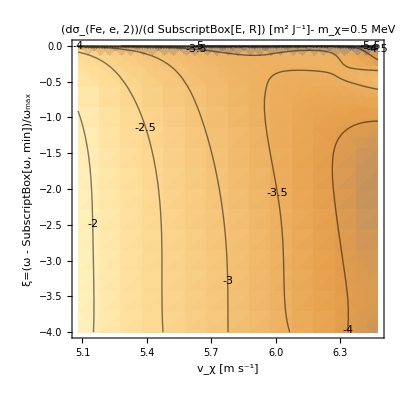

Compare to the above plot, checking the ω scale

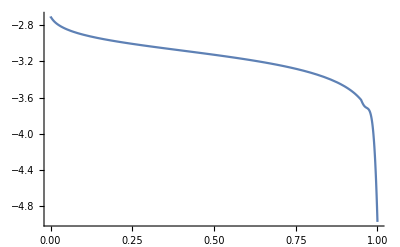

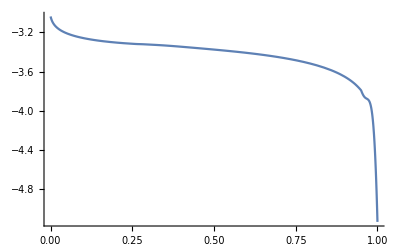

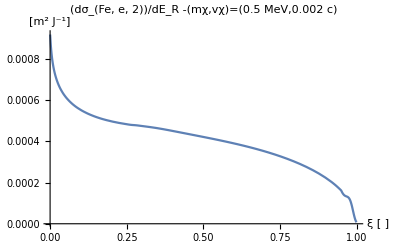

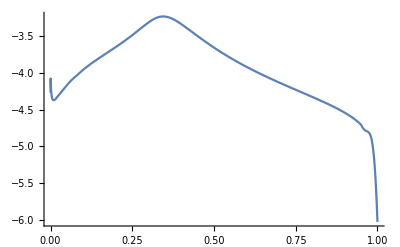

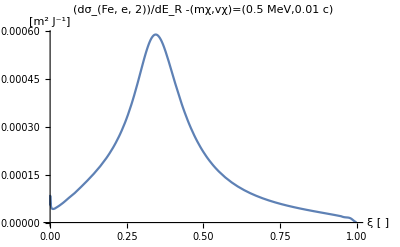

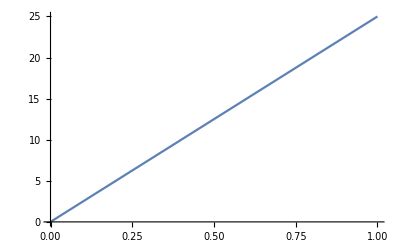

```mathematica
vχbounds=testkinσinterpolateξmeosc2higherres[["vχ"]];
ξbounds=testkinσinterpolateξmeosc2higherres[["ξ"]];
Show[{DensityPlot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
Print["Compare to the above plot, checking the ω scale"]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][5.6,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][5.8,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[10^testkinσinterpolateξmeosc2higherres[["dσf"]][5.8,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All,PlotLabel->"(dσ_(Fe, e, 2))/dE_R -(mχ,vχ)=(0.5 MeV,0.002 c)",AxesLabel->{"ξ [ ]","[m^2 J^-1]"}]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχbounds[[2]],Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχbounds[[2]],Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All,PlotLabel->"(dσ_(Fe, e, 2))/dE_R -(mχ,vχ)=(0.5 MeV,0.01 c)",AxesLabel->{"ξ [ ]","[m^2 J^-1]"}]
Plot[(("ℏ")/("JpereV")/.SIConstRepl)ωofξandvχ[ξ,testkinσinterpolateξmeosc2higherres[["ωmin"]],10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
(*Plot[(("ℏ")/("JpereV")/.SIConstRepl)ξofωandvχ[ω,testkinσinterpolateξmeosc2higherres[["ωmin"]],10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]],{ω,10^ξbounds[[1]],10^ξbounds[[2]]}]*)
```

```mathematica
("JpereV"/.SIConstRepl)
```

1.602×10^-19

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000141826}. NIntegrate obtained 0.000132359 and 2.63987×10^-6 for the integral and error estimates.

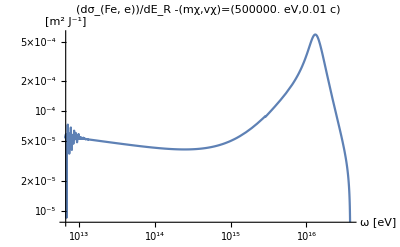

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000149062}. NIntegrate obtained 0.000143482 and 1.97166×10^-6 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp,ERmintemp},
mχtemp = testkinσinterpolateξmeosc2higherres[["mχ"]];
vχtemp = 10^testkinσinterpolateξmeosc2higherres[["vχ"]][[2]];
ERmaxtemp = ωmaxofvχ[10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]];
ERmintemp = testkinσinterpolateξmeosc2higherres[["ωmin"]];
Print[LogLogPlot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Plot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000334144122406762993635932768032859030427061952650547027587890625}. NIntegrate obtained 0.000097441 and 1.80677×10^-9 for the integral and error estimates.

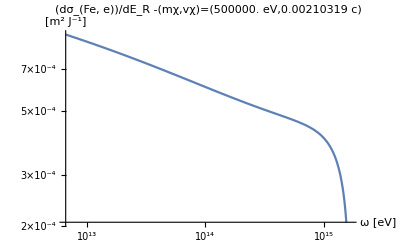

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003356319043151438107400706678529189730397774837911128997802734375}. NIntegrate obtained 0.0000978685 and 2.73029×10^-9 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp,ERmintemp},
mχtemp = testkinσinterpolateξmeosc2higherres[["mχ"]];
vχtemp = 10^(5.8);
ERmaxtemp = ωmaxofvχ[vχtemp,testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]];
ERmintemp = testkinσinterpolateξmeosc2higherres[["ωmin"]];
Print[LogLogPlot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Plot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

#### Recoil Energy Probability

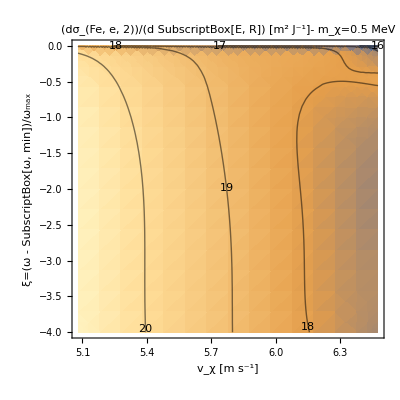

```mathematica
Show[{DensityPlot[Log10[(("ne"/.FeλeDictOscillators[[2]]["fitparams"])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[Log10[(("ne"/.FeλeDictOscillators[[2]]["fitparams"])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

This looks like it is missing a factor of ℏ

```mathematica
(("ne"/.FeλeDictOscillators[[2]]["fitparams"][[1]])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])/.vχ->0.9vχbounds[[2]]
NIntegrate[%,{ξ,0,1}]
% "ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]
%(ωmaxofvχ[10^(0.9vχbounds[[2]]),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])
Print["This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ"]
```

1.91532×10^29 10^(-7.27767+InterpolatingFunction[…][5.82941,ξ])

5.93707×10^14

6.26361×10^-20

0.000120022

This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ

```mathematica
(("ne"/.FeλeDictOscillators[[2]]["fitparams"][[1]])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])/.vχ->vχbounds[[1]]
% "ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]
%(ωmaxofvχ[10^(vχbounds[[1]]),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])
NIntegrate[%,{ξ,0,1}]
Print["This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ"]
vχbounds[[1]]
```

1.91532×10^29 10^(-6.81987+InterpolatingFunction[…][Log[120000]/Log[10],ξ])

0.0000202066 10^(-6.81987+InterpolatingFunction[…][Log[120000]/Log[10],ξ])

1.0942×10^9 10^(-6.81987+InterpolatingFunction[…][Log[120000]/Log[10],ξ])

0.0000934931

This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ

Log[120000]/Log[10]

2.2191×10^-18 10^(-7.7942+InterpolatingFunction[…][6.34898,Log[ξ]/Log[10]])

7.98093×10^-30

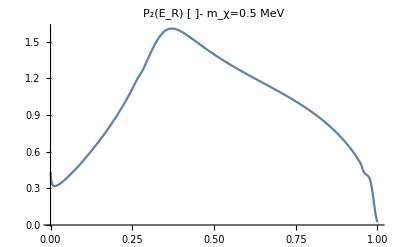

1.

```mathematica
10^Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])(ωmaxofvχ[10^(vχ),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])"ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]]/.vχ->1.25 vχbounds[[1]]
NIntegrate[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
Plot[(%%)/%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(E_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[(%%%)/(%%),{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

4.27038×10^11 10^(-7.79507+InterpolatingFunction[…][6.35,Log[ξ]/Log[10]])

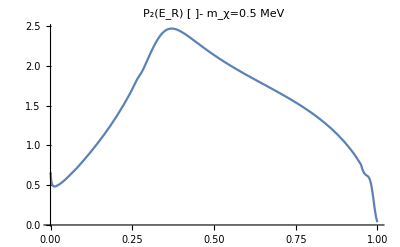

1.52955

```mathematica
10^Log10[(("ne"/.FeλeDictOscillators[[2]]["fitparams"][[1]])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])(ωmaxofvχ[10^(vχ),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])"ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]]/.vχ->6.35
Plot[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(E_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[%%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

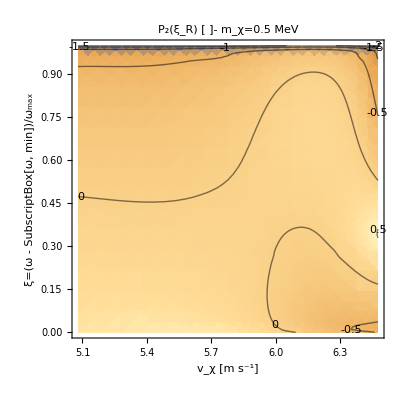

```mathematica
Show[{DensityPlot[Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(ξ_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

```mathematica
ftest[ξ_]:=ξ^2
gtest[ξ_]:= Log[ξ]
htest[ξ_]:= (ftest[#]/gtest[#])&[ξ]
```

```mathematica
htest[ξ]
```

ξ^2/Log[ξ]

```mathematica
Ptest[vχ_,ξ_]:=(10^testkinσinterpolateξmeosc2higherres[["dσf"]][#1,#2]/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][#1,ξt],{ξt,ξbounds[[1]],ξbounds[[2]]}])&[vχ,ξ]
```

```mathematica
Ptest[vχbounds[[2]]0.99,-3]
```

0.174541